```mathematica
Clear[particleCoordinates, particleForces, particleForcesAndEnergies, particlePositions, rlist]
```

## Constraints

### overlapC

#### Definitions

```mathematica
overlapC[{{x1_, y1_}, r1_}, {{x2_, y2_}, r2_}]:=
((r2+r1)^2≤(y2-y1)^2+(x2-x1)^2)
```

#### Testing

```mathematica
overlapC[{{1,1},1}, {{0,0},.5}]
```

False

### borderC

#### Definitions

```mathematica
borderC[{x_, y_}, r_, size_]:=And[
size-r≥x, size-r≥y,r≤x, r≤y
]
```

#### Testing

```mathematica
borderC[{1,1},1, 2]
```

True

## Initialization

### createDisk

Randomly obtains disk coordinates that satisfy constraints.

#### Definition

```mathematica
createDisk[circles_List,radii_List, size_]:=Module[
{cnumber=circles//Length, position, riffled, count=0, insert=False, rc, r},

(*splice radii list, select next*)
rc=radii⟦;;cnumber⟧;
r=radii⟦cnumber+1⟧;
riffled=Riffle[circles,rc]//Partition[#, 2]&;

(*testing loop*)
While[
(*stop when inserted or overcount*)
And[count<100, !insert ],
	position=RandomReal[{0, size}, 2];

(*if doesn't overlap border or overlap other circle*)
	
	If[And[
	borderC[position,r,size],
	And@@(overlapC[{position, r}, #]&/@riffled)
	],
	insert=True;
	];
count=count+1;
];
If[count==100, Print["fail"]];

position
]
```

#### testing

```mathematica
createDisk[{{1,1}, {2,2}}, {.5,.4, 1}, 3]
```

{0.0516464,-1.55097}

### createDisks

Randomly generates initial coordinates for the set of radii.

#### Definitions

```mathematica
createDisks[radii_List, size_]:=Module[
{coordinates, number=radii//Length},
coordinates={createDisk[{}, radii, size]};
Nest[Join[#,{createDisk[#, radii, size]}]&, coordinates, number-1]
]
```

#### testing

```mathematica
rlist={1,1,1,.5,.5,.5,.5}
```

{1,1,1,0.5,0.5,0.5,0.5}

```mathematica
c=createDisks[{1,1,1,.5,.5,.5,.5}, 10]
```

{{4.1868,3.91132},{1.76111,5.72076},{7.10307,3.07754},{9.44668,7.56415},{0.804215,4.01887},{5.27596,7.84833},{4.07542,7.99407}}

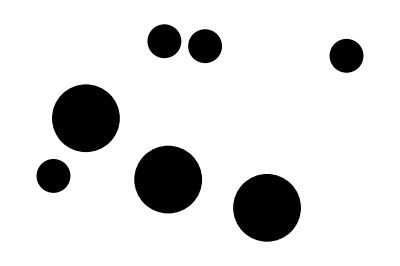

```mathematica
displayParticles[%, {1,1,1,.5,.5,.5,.5}]
```

```mathematica
rifle=Riffle[c, rlist]
```

{{71.9279,22.9072},1,{89.9967,34.8854},1,{69.204,16.2737},1,{8.22367,87.2121},0.5,{79.9361,95.9861},0.5,{27.2723,1.25093},0.5,{15.4628,40.5759},0.5}

```mathematica
displayParticles[positions_, radiuslist_, opts:OptionsPattern[]]:=
Module[
{rifflelist=Riffle[positions, radiuslist]//Partition[#, 2]&},
Show[Graphics[{
Disk[#[[1]], #[[2]]]&/@rifflelist}] ,
 Evaluate[FilterRules[{opts}, Options[Graphics]]]]
]
```

### velocityInit

#### Definitions

```mathematica
velocityInit[size_,number_]:=RandomReal[size{-1, 1}, number]
```

#### Testing

```mathematica
velocityInit[5]
```

{-0.868833,-0.560377,-0.0372914,0.866285,0.197821}

### setInitialEvents

Initializing all events to checks. Events are defined by triples: {timestamp, i, j}. Need to insert into minHeap still.

#### Definitions

```mathematica
setInitialEvents[N_,H_, gtime_:0]:=Block[
{events},
events=Table[{gtime, i, Infinity}, {i, N}];
]
```

## Dynamics

```mathematica
velocityVerlet[{positions_, oldVelocities_,oldForces_}, dt_, radiuslist_] :=
Block[
{deltaPositions,newpositions,newVelocities,newForces},
deltaPositions = oldVelocities dt + 0.5 oldForces dt^2;
newpositions = positions + deltaPositions;
newForces=particleForces[newpositions, radiuslist];
newVelocities =  oldVelocities + 0.5(oldForces + newForces)dt;
{newpositions,newVelocities,newForces}
]
```

```mathematica
particleForces[positions_ , radiuslist_]:= 
Block[
{augmentedDM, differenceMat, radiusMat},
radiusMat=Outer[Plus, radiuslist,radiuslist];
augmentedDM = DistanceMatrix[positions, DistanceFunction->SquaredEuclideanDistance]+.1;
differenceMat =  Outer[Subtract, positions, positions,1];
Total[-1200differenceMat ((2radiusMat)^3-augmentedDM^3)/augmentedDM^7]
]
```

```mathematica
particleForces[positions_ , radiuslist_]:= 
Block[
{augmentedDM, differenceMat, radiusMat},
radiusMat=Outer[Plus, radiuslist,radiuslist];
augmentedDM = DistanceMatrix[positions, DistanceFunction->SquaredEuclideanDistance]/.n_/;n<2.2->.99;
differenceMat =  Outer[Subtract, positions, positions,1];
Total[-1200differenceMat (1-augmentedDM^3)/augmentedDM^7]
]
```

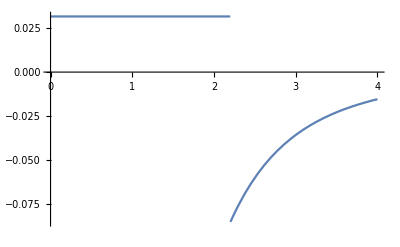

```mathematica
Plot[If[d>2.2, ((1-d^3)/d^6),(1-.99^3)/.99^6] ,{d, 0, 4}]
```

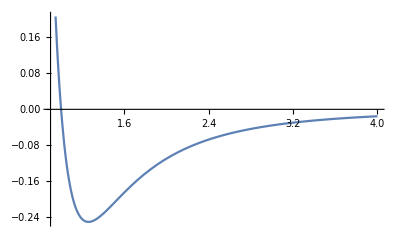

```mathematica
Plot[(1-d^3)/d^6, {d, .9, 4}]
```

## Visualization

```mathematica
rlist={1,1,1,1,1,1,1,1,1, .8, .8, .8, .8, .8, .8};
```

```mathematica
particlePositions=createDisks[rlist, 15]
forces = particleForces[particlePositions, rlist];
velocities = ConstantArray[{0,0},Length[particlePositions]];
```

{{4.95689,9.86426},{12.4373,0.930322},{4.43313,4.31927},{2.03275,14.6783},{13.1878,12.1133},{9.33103,0.15711},{10.0181,10.7312},{13.601,4.57687},{12.6775,11.0534},{4.42121,11.3666},{12.1297,3.43788},{14.0469,3.72143},{8.9559,13.2533},{4.19623,12.052},{1.27591,8.0241}}

```mathematica
displayParticles[positions_, radiuslist_, opts:OptionsPattern[]]:=
Module[
{rifflelist=Riffle[positions, rlist]//Partition[#, 2]&},
Show[Graphics[{
Disk[#[[1]], #[[2]]]&/@rifflelist}] ,
 Evaluate[FilterRules[{opts}, Options[Graphics]]]]
]
```

```mathematica
Dynamic[displayParticles[particlePositions, rlist,PlotRange->{{-5,20},{-5,20}},Frame->True,ImageSize->Medium]]
```

```mathematica
Do[{particlePositions,velocities,forces}=velocityVerlet[{particlePositions, velocities,forces}, 0.001, rlist];FinishDynamic[],{1000}]
```

```mathematica
forces
```

{{-3117.19,-3117.19},{-3117.19,-3117.19},{-3117.19,-3117.19},{-3117.19,-3117.19},{-3117.19,-3117.19},{-3117.19,-3117.19},{-3117.19,-3117.19},{-3117.19,-3117.19},{-3117.19,-3117.19},{-11542.1,-11542.1},{-11542.1,-11542.1},{-11542.1,-11542.1},{-11542.1,-11542.1},{-11542.1,-11542.1},{-11542.1,-11542.1}}

```mathematica
DistanceMatrix[particlePositions, particlePositions]//Abs
```

{{0.,6.71723,1.36116,9.44221,12.1542,22.1305,11.6411,10.5793,17.9967,14.5122,12.8812,9.54821,13.2906,3.92925,4.29799},{6.71723,0.,6.74574,12.9985,9.75783,16.6837,15.5828,11.9164,17.301,16.0914,14.2828,3.81723,14.4761,6.28063,4.11517},{1.36116,6.74574,0.,8.18091,11.025,21.3795,10.4593,9.21863,16.6684,13.1581,11.5213,9.96079,11.9296,2.67881,5.14161},{9.44221,12.9985,8.18091,0.,9.87094,21.7789,2.59753,3.97068,11.2596,5.91187,4.899,16.7883,5.44335,6.87702,13.0978},{12.1542,9.75783,11.025,9.87094,0.,11.916,11.9331,6.19649,7.77448,8.89232,7.43274,12.8814,7.26658,8.37565,12.8472},{22.1305,16.6837,21.3795,21.7789,11.916,0.,23.7297,17.9881,15.1667,19.618,18.6469,17.3878,18.3047,19.0948,20.7902},{11.6411,15.5828,10.4593,2.59753,11.9331,23.7297,0.,5.75082,11.8012,5.8253,5.59944,19.3633,6.10828,9.41129,15.4993},{10.5793,11.9164,9.21863,3.97068,6.19649,17.9881,5.75082,0.,7.84901,4.21527,2.42478,15.691,2.74779,6.93337,13.2622},{17.9967,17.301,16.6684,11.2596,7.77448,15.1667,11.8012,7.84901,0.,6.07024,6.38461,20.6141,5.83866,14.103,19.8391},{14.5122,16.0914,13.1581,5.91187,8.89232,19.618,5.8253,4.21527,6.07024,0.,1.80878,19.8383,1.69726,11.0582,17.4417},{12.8812,14.2828,11.5213,4.899,7.43274,18.6469,5.59944,2.42478,6.38461,1.80878,0.,18.0322,0.546426,9.32823,15.682},{9.54821,3.81723,9.96079,16.7883,12.8814,17.3878,19.3633,15.691,20.6141,19.8383,18.0322,0.,18.2007,9.99173,5.60778},{13.2906,14.4761,11.9296,5.44335,7.26658,18.3047,6.10828,2.74779,5.83866,1.69726,0.546426,18.2007,0.,9.68103,15.9983},{3.92925,6.28063,2.67881,6.87702,8.37565,19.0948,9.41129,6.93337,14.103,11.0582,9.32823,9.99173,9.68103,0.,6.4211},{4.29799,4.11517,5.14161,13.0978,12.8472,20.7902,15.4993,13.2622,19.8391,17.4417,15.682,5.60778,15.9983,6.4211,0.}}